## Power-law

```mathematica
f0=10^-2.83728;
α0=1.0179;
Mf0=10.838;
i0=30;
j0=10;
```

## mass function

```mathematica
Pcc[m_,α_,Mf_]:=(Mf^(-1-α) α^2)/Gamma[1/α] m^α ⅇ^(-(m/Mf )^α)
Integrate[Pcc[m,α,Mf],{m,0,∞},Assumptions->{α>0,Mf>0}]
```

1

```mathematica
NIntegrate[Pcc[m,0.9,10.0],{m,10^-1,10^3}]
```

0.999929

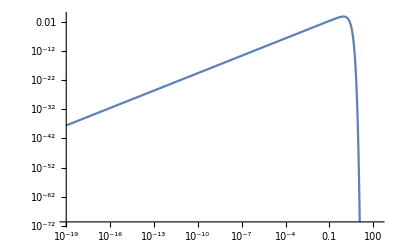

```mathematica
LogLogPlot[Pcc[m,2, 0.9], {m,10^-19,200}]
```

## m_pbh

```mathematica
1/Integrate[Pcc[i,α,Mf]/i,{i,0,∞},Assumptions->{α>0,Mf>0}]
mpbh[α_,Mf_]:=(Mf Gamma[1/α])/α
```

(Mf Gamma[1/α])/α

## F(m)

```mathematica
F[i_,α_,Mf_]:=Pcc[i,α,Mf]*mpbh[α,Mf]/i;
F[i,α,Mf]
```

ⅇ^(-(i/Mf)^α) i^(-1+α) Mf^-α α

```mathematica
Integrate[F[i,α,M],{i,0,∞},Assumptions->{α>0,Mf>0}]//PowerExpand
```

1

## R1

```mathematica
1.32*10^6*(f/mpbh[α,Mf])^(53/37)l^(-21/37)(i*j)^(3/37)*(i+j)^(36/37)F[i,α,Mf]*F[j,α,Mf]*F[l,α,Mf]//Simplify
```

(1.32×10^6 ⅇ^(-(i/Mf)^α-(j/Mf)^α-(l/Mf)^α) i^α j^α (i+j)^(36/37) l^(-58/37+α) Mf^(-3 α) α^3 ((f α)/(Mf Gamma[1/α]))^(53/37))/(i j)^(34/37)

```mathematica
Integrate[  l^(-58/37+α)ⅇ^(-(l/Mf)^α),{l,10^-1,10^3},Assumptions->{α>0,Mf>0}]
```

(Mf^(-21/37+α) (Gamma[1-21/(37 α),10^-α Mf^-α]-Gamma[1-21/(37 α),1000^α Mf^-α]))/α

```mathematica
1/α Mf^(-21/37+α) (Gamma[1-21/(37 α),10^-α Mf^-α]-Gamma[1-21/(37 α),1000^α Mf^-α])/.{α->11/37,Mf->9.34}
```

3.34968

```mathematica
Integrate[l^(-21/37)F[l,α,Mf],{l,10^-1,10^3},Assumptions->{α>0,Mf>0}]
```

(Gamma[1-21/(37 α),10^-α Mf^-α]-Gamma[1-21/(37 α),1000^α Mf^-α])/Mf^(21/37)

```mathematica
Integrate[l^(-21/37)F[l,α,Mf],{l,0,∞},Assumptions->{α>21/37,Mf>0}]
```

Gamma[1-21/(37 α)]/Mf^(21/37)

```mathematica
1.32*10^6*(f/mpbh[α,Mf])^(53/37)(Gamma[1-21/(37 α),10^-α Mf^-α]-Gamma[1-21/(37 α),1000^α Mf^-α])/Mf^(21/37)*(i*j)^(3/37)*(i+j)^(36/37)F[i,α,Mf]*F[j,α,Mf]//Simplify
```

1/(i j)^(34/37)1.32×10^6 ⅇ^(-(i/Mf)^α-(j/Mf)^α) i^α j^α (i+j)^(36/37) Mf^(-21/37-2 α) α^2 ((f α)/(Mf Gamma[1/α]))^(53/37) (Gamma[1-21/(37 α),10^-α Mf^-α]-Gamma[1-21/(37 α),1000^α Mf^-α])

```mathematica
Clear[i,mergerRateDensity1st]
mergerRateDensity1st[f_,i_,j_,α_,Mf_]:=1/(i j)^(34/37)1.32*^6 ⅇ^(-(i/Mf)^α-(j/Mf)^α) i^α j^α (i+j)^(36/37) Mf^(-21/37-2 α) α^2 ((f α)/(Mf Gamma[1/α]))^(53/37) (Gamma[1-21/(37 α),10^-α Mf^-α]-Gamma[1-21/(37 α),1000^α Mf^-α])
```

```mathematica
mergerRateDensity1st[f0,i0,j0,3,Mf0]
```

0.0179609

```mathematica
{f0,i0,j0,α0,Mf0}
```

{1/1000,30,10,2.85,10}

```mathematica
l^(-21/37)F[l,α,Mf]
```

ⅇ^(-(l/Mf)^α) l^(-58/37+α) Mf^-α α

## R2

```mathematica
Integrate[l^(-42/37)*F[l,α,Mf],{l,0,∞},Assumptions->{α>21/37,Mf>0}]
```

ConditionalExpression[Gamma[1-42/(37 α)]/Mf^(42/37), α>42/37]

```mathematica
Integrate[l^(-42/37)*F[l,α,Mf],{l,10^-1,10^3},Assumptions->{α>0,Mf>0}]
```

(Gamma[1-42/(37 α),10^-α Mf^-α]-Gamma[1-42/(37 α),1000^α Mf^-α])/Mf^(42/37)

```mathematica
mergerRateDensity2nd01[f_,i_,j_,k_,α_,Mf_]:=1.59*10^4*(f/mpbh[α,Mf])^(69/37)k^(6/37)(Gamma[1-42/(37 α),10^-α Mf^-α]-Gamma[1-42/(37 α),1000^α Mf^-α])/Mf^(42/37)(i+j)^(6/37)(i+j+k)^(72/37)F[i,α,Mf]*F[j,α,Mf]*F[k,α,Mf]
```

```mathematica
mergerRateDensity2nd01[f,i-e,e,j,α,Mf]
```

1/Mf^(42/37)15900. i^(6/37) j^(6/37) (i+j)^(72/37) F[e,α,Mf] F[-e+i,α,Mf] F[j,α,Mf] (Gamma[1-42/(37 α),10^-α Mf^-α]-Gamma[1-42/(37 α),1000^α Mf^-α]) (f/mpbh[α,Mf])^(69/37)

```mathematica
mergerRateDensity2nd0[f_?NumericQ,i_?NumericQ,j_?NumericQ,e_?NumericQ,α_?NumericQ,Mf_?NumericQ]:=15900. e^(-1+α) ⅇ^(-(e/Mf)^α-((-e+i)/Mf)^α-(j/Mf)^α) i^(6/37) (-e+i)^(-1+α) j^(-31/37+α) (i+j)^(72/37) Mf^(-42/37-3 α) α^3 ((f α)/(Mf Gamma[1/α]))^(69/37) (Gamma[1-42/(37 α),10^-α Mf^-α]-Gamma[1-42/(37 α),1000^α Mf^-α])
```

```mathematica
mergerRateDensity2nd1[f_?NumericQ,i_?NumericQ,j_?NumericQ,α_?NumericQ,Mf_?NumericQ]:=15900.  ⅇ^(-(j/Mf)^α)i^(6/37)  (i+j)^(72/37) Mf^(-42/37-3 α) α^3 ((f α)/(Mf Gamma[1/α]))^(69/37) (Gamma[1-42/(37 α),10^-α Mf^-α]-Gamma[1-42/(37 α),1000^α Mf^-α])NIntegrate[e^(-1+α) ⅇ^(-(e/Mf)^α-((-e+i)/Mf)^α)(-e+i)^(-1+α) j^(-31/37+α),{e,10^-1,i},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

```mathematica
Clear[mergerRateDensity2nd];
mergerRateDensity2nd[f_?NumericQ,i_?NumericQ,j_?NumericQ,α_?NumericQ,Mf_?NumericQ]:=1/2(mergerRateDensity2nd1[f,i,j,α,Mf]+mergerRateDensity2nd1[f,j,i,α,Mf])
```

```mathematica
mergerRateDensity2nd[f0,i0,j0,α0,Mf0]
```

0.000744672

```mathematica
ratioR[f_?NumericQ,i_?NumericQ,j_?NumericQ,α_?NumericQ,Mf_?NumericQ]:=mergerRateDensity2nd[f,i,j,α,Mf]/mergerRateDensity1st[f,i,j,α,Mf];
```

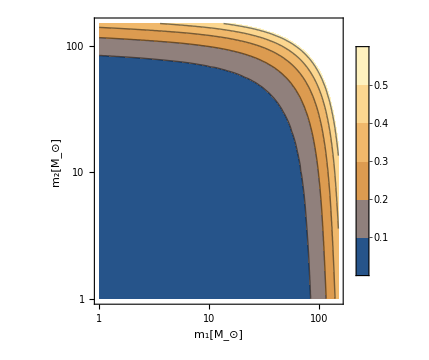

```mathematica
mMin=1;
mMax=150;

ContourPlot[ratioR[f0,i,j,α0,Mf0],{i,mMin,mMax},{j,mMin,mMax},FrameLabel->{"m_1[M_⊙]","m_2[M_⊙]"},ScalingFunctions->{"Log","Log"},FrameStyle->FontFamily->"Times",BaseStyle->FontSize->14,LabelStyle->GrayLevel[0],Frame->True,Axes->False,PlotRangePadding->None,ImageSize->360,AspectRatio->1,PlotLegends->Automatic]
(*Export["../latex/ratio-log.pdf",%]*)
```

```mathematica
Integrate[e^(-1+α) ⅇ^(-(e/Mf)^α-((-e+i)/Mf)^α-(j/Mf)^α)  (-e+i)^(-1+α) ,{e,10^-1,i},Assumptions->{α>0,Mf>0,i>0}]
```

Integrate[e^(-1+α) ⅇ^(-(e/Mf)^α-((-e+i)/Mf)^α-(j/Mf)^α) (-e+i)^(-1+α),{e,1/10,i},Assumptions→{α>0,Mf>0,i>0}]

```mathematica
mergerRateDensity2nd00[f_,i_,j_,k_,l_,α_,Mf_]:=1.59*10^4*(f/mpbh[α,Mf])^(69/37)k^(6/37)l^(-42/37)*F[l,α,Mf](i+j)^(6/37)(i+j+k)^(72/37)F[i,α,Mf]*F[j,α,Mf]*F[k,α,Mf]
```

```mathematica
mergerRateDensity2nd00[f,i-e,e,j,l,α,Mf]
```

15900. e^(-1+α) ⅇ^(-(e/Mf)^α-((-e+i)/Mf)^α-(j/Mf)^α-(l/Mf)^α) i^(6/37) (-e+i)^(-1+α) j^(-31/37+α) (i+j)^(72/37) l^(-79/37+α) Mf^(-4 α) α^4 ((f α)/(Mf Gamma[1/α]))^(69/37)